```mathematica
(*Алгаритм Грэхама*)
PolygonBilder[points_]:=Block[{
P = List[],
Pl = List[],Pr = List[],
Sl = List[], Sr= List[],
PlPoint , PrPoint,
length,n,
result
},
length = Length[points];
PlPoint = Part[points,1];
PrPoint =Part[points,1];

(*находим минимумальную и максимальную по иксам точку*)
For[n = 2, n ≤  length,++n,

If[Part[Part[points,n],1]<Part[PlPoint,1],PlPoint =Part[points,n]];
If[Part[Part[points,n],1]>Part[PrPoint,1],PrPoint =Part[points,n]];
];

(*делим множество на два подмножества*)
For[n = 1, n ≤  length,++n,
If[Part[points, n]== PlPoint ||Part[points, n]== PrPoint,,
If[Det[{PrPoint-PlPoint,Part[points, n]-PlPoint }]<0,AppendTo[Pr,Part[points, n]], AppendTo[Pl,Part[points, n]]]
];
];

(*вернем точки а то не хо*)
AppendTo[Pr, PlPoint];
AppendTo[Pl, PrPoint];


(*упорядочиваем*)
Pr = SortBy[Pr, First];
Pl= SortBy[Pl, First];
(*построение выпуклой оболочки для множества Pl*)
length = Length[Pl];
AppendTo[Sl, PlPoint];
For[n = 1, n ≤  length,++n,
If[Length[Sl]== 1,AppendTo[Sl,Part[Pl,n]],
If[Det[{Part[Sl, Length[Sl]]-Part[Sl, Length[Sl]-1],Part[Pl, n]-Part[Sl, Length[Sl]-1] }]≤ 0,
 AppendTo[Sl,Part[Pl,n]];,
 Sl = Delete[Sl, Length[Sl]]; n--;
];
];
];
(*построение выпуклой оболочки для множества Pr*)
length = Length[Pr];
AppendTo[Sr, PrPoint];
For[n = length,   1≤ n,--n,
If[Length[Sr]== 1,AppendTo[Sr,Part[Pr,n]],
If[Det[{Part[Sr, Length[Sr]]-Part[Sr, Length[Sr]-1],Part[Pr, n]-Part[Sr, Length[Sr]-1] }]< 0,
 AppendTo[Sr,Part[Pr,n]];,
 Sr = Delete[Sr, Length[Sr]]; n++;
];
];
];


Sr = Delete[Sr, 1];
result = Join[Sl,Sr];


Return[result]]
```

```mathematica
KickPoints[polygon_]:=Block[{
},
Return[Complement[points,polygon]]
]
```

```mathematica
Test[p1_,p2_,p3_,p4_] := Block[{
result,
α, β, k
},
α =((p2[[1]]-p1[[1]])*(p4[[1]]-p1[[1]]) +(p2[[2]]-p1[[2]])*(p4[[2]]-p1[[2]]));
β =((p2[[1]]-p3[[1]])*(p4[[1]]-p3[[1]]) +(p2[[2]]-p3[[2]])*(p4[[2]]-p3[[2]]));

If[α>0 &&β > 0, result =True,
If[α<0 &&β < 0, result =False,
k = Abs[(p2[[1]]-p1[[1]])*(p4[[2]]-p1[[2]])-(p4[[1]]-p1[[1]])*(p2[[2]]-p1[[2]])]*β 
+ α* Abs[(p2[[1]]-p3[[1]])*(p4[[2]]-p3[[2]])-(p4[[1]]-p3[[1]])*(p2[[2]]-p3[[2]])];
result = k≥0;
];
];
Return[result]
]

Flip[index_] :=Block[{
segmentN,
triangle1,triangle2,
t1i,t2i,
temp1,temp2
},

t1i =st[[index]][[1]];
t2i = st[[index]][[2]];
triangle1 = triangles[[t1i]];
triangle2 = triangles[[t2i]];

triangle1 = Complement[triangle1,{index}];
triangle2 = Complement[triangle2,{index}];

temp1 = Intersection[segments[[triangle1[[1]]]],segments[[triangle1[[2]]]]];
temp2 = Intersection[segments[[triangle2[[1]]]],segments[[triangle2[[2]]]]];

segmentN ={Flatten[temp1,1], Flatten[temp2,1]};

temp1 = triangle1;
temp2 =triangle2;
If[ Length[Intersection[segments[[triangle2[[1]]]],segments[[triangle1[[2]]]]]]== 1
,
triangle1 = {temp1[[1]],temp2[[2]],index};
triangle2 = {temp2[[1]],temp1[[2]],index};
(*Print["temp2[2].st = ",st[[temp2[[2]]]]];
Print["temp1[2].st = ",st[[temp1[[2]]]]];*)
st[[temp2[[2]]]]=Append[Complement[st[[temp2[[2]]]], {t2i}],t1i];
st[[temp1[[2]]]]=Append[Complement[st[[temp1[[2]]]], {t1i}],t2i];
,
triangle1 = {temp1[[1]],temp2[[1]],index};
triangle2 = {temp2[[2]],temp1[[2]],index};

st[[temp2[[1]]]]=Append[Complement[st[[temp2[[1]]]],{ t2i}],t1i];
st[[temp1[[2]]]]=Append[Complement[st[[temp1[[2]]]], {t1i}],t2i];
];

segments [[index]] = segmentN;
triangles[[t1i]] = triangle1;
triangles[[t2i]] = triangle2;


]
```

```mathematica
CheckStart[] := Block[{
triangle,stemp,tresult,
triangle2,triangle1,
temp1,temp2,end = False,
i,n
},
While[!end,
end = True;
For[i = 1,i ≤  Length[triangles],i++,
triangle = triangles[[i]];
For[n = 1,n ≤  Length[triangle],n++,

stemp = st[[triangle[[n]]]];
If[Length[stemp]== 2,
triangle1 = triangles[[stemp[[1]]]];
triangle2 =  triangles[[stemp[[2]]]];
triangle1 = Complement[triangle1,{triangle[[n]]}];
triangle2 = Complement[triangle2,{triangle[[n]]}];

temp1 = Intersection[segments[[triangle1[[1]]]],segments[[triangle1[[2]]]]];
temp2 = Intersection[segments[[triangle2[[1]]]],segments[[triangle2[[2]]]]];
tresult = Test[Flatten[temp1,1],segments[[triangle[[n]]]][[1]], Flatten[temp2,1],segments[[triangle[[n]]]][[2]]];
If[tresult,
(*flags[[i]] = True;*)
,
Flip[triangle[[n]]];
end =False;
];

];
];
];
];

]
```

```mathematica
Triangulation[] := Block[{
polygon,
pointsN,
result,

i,leng
},
polygon = PolygonBilder[points];
polygon = Delete[polygon, Length[polygon]];
pointsN =KickPoints[polygon];

leng = Length[polygon];
For[i = 1, i < leng,i++,
AppendTo[segments,{polygon[[i]],polygon[[i+1]]}];
];
AppendTo[segments,{polygon[[leng]],polygon[[1]]}];

For[i=1, i ≤  leng, i++,
AppendTo[segments,{polygon[[i]],pointsN[[1]]}];
];

For[i=1, i <  leng, i++,
AppendTo[triangles,{i, leng+i, leng+i+1}];
];
AppendTo[triangles,{i, leng*2, leng+1}];

For[i=1, i ≤ leng, i++,
AppendTo[st,{i}];
];
AppendTo[st,{leng,1}];
For[i=2, i ≤  leng, i++,
AppendTo[st,{i-1,i}];
];

CheckStart[];

For[i = 2,  i≤ Length[pointsN],i++,

];

Print[segments];
Print[triangles];
Print[st];
Return[result]
]
```

{{{22,901},{227,928}},{{227,928},{778,785}},{{778,785},{795,747}},{{795,747},{904,437}},{{904,437},{888,204}},{{888,204},{755,82}},{{755,82},{175,128}},{{175,128},{22,901}},{{22,901},{141,857}},{{227,928},{141,857}},{{227,928},{795,747}},{{795,747},{141,857}},{{795,747},{175,128}},{{904,437},{755,82}},{{904,437},{175,128}},{{175,128},{141,857}}}

{{1,9,10},{2,3,11},{12,10,11},{4,15,13},{5,6,14},{16,12,13},{7,14,15},{8,16,9}}

{{1},{2},{2},{4},{5},{5},{7},{8},{8,1},{1,3},{2,3},{3,6},{4,6},{5,7},{7,4},{8,6}}

result

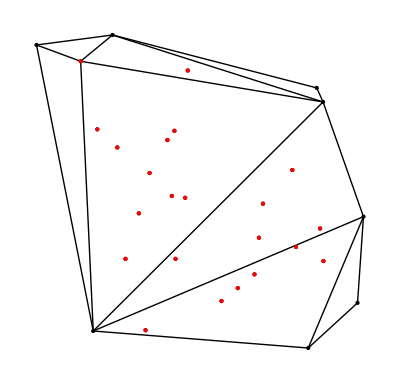

```mathematica
points= Table[{RandomInteger[{0, 1000}],RandomInteger[{0, 1000}]},{30}];
segments= List[];
triangles= List[];
st= List[];
flags= List[];
Triangulation[]

Graphics[{Line[segments], Point[points],Red, Point[KickPoints[PolygonBilder[points]]]}]
```

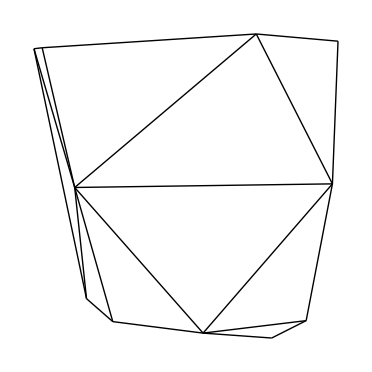

{{1,11,12},{2,12,13},{3,4,14},{15,13,14},{5,17,16},{15,18,17},{7,6,16},{8,18,19},{9,19,20},{10,20,11}}

{{1},{2},{3},{3},{5},{7},{7},{8},{9},{10},{10,1},{1,2},{2,4},{3,4},{4,6},{5,7},{6,5},{8,6},{8,9},{9,10}}

{{{11,939},{36,942}},{{36,942},{688,984}},{{688,984},{937,962}},{{937,962},{920,527}},{{920,527},{840,110}},{{840,110},{735,57}},{{735,57},{526,72}},{{526,72},{251,107}},{{251,107},{171,177}},{{171,177},{11,939}},{{11,939},{135,516}},{{36,942},{135,516}},{{688,984},{135,516}},{{688,984},{920,527}},{{920,527},{135,516}},{{840,110},{526,72}},{{920,527},{526,72}},{{526,72},{135,516}},{{251,107},{135,516}},{{171,177},{135,516}}}

```mathematica
CheckStart[] 
Graphics[{Line[segments]}]
triangles
st
segments
```

```mathematica
ns = segments
nt = triangles
st2 = st

segments[[13]]
segments[[14]]
segments[[15]]
segments[[16]]
segments[[17]]
st[[11]]
st[[12]]
st[[13]]
st[[14]]
st[[15]]
st[[16]]
st[[17]]
triangles[[10]]
triangles[[1]]
```

{{{75,622},{198,889}},{{198,889},{364,997}},{{364,997},{974,986}},{{974,986},{944,538}},{{944,538},{758,226}},{{758,226},{393,66}},{{393,66},{189,36}},{{189,36},{84,210}},{{84,210},{75,622}},{{75,622},{75,622}},{{75,622},{98,398}},{{198,889},{98,398}},{{364,997},{98,398}},{{974,986},{98,398}},{{944,538},{98,398}},{{758,226},{98,398}},{{393,66},{98,398}},{{189,36},{98,398}},{{84,210},{98,398}},{{75,622},{98,398}}}

{{1,11,12},{2,12,13},{3,13,14},{4,14,15},{5,15,16},{6,16,17},{7,17,18},{8,18,19},{9,19,20},{10,20,11}}

{{1},{2},{3},{4},{5},{6},{7},{8},{9},{10},{10,1},{1,2},{2,3},{3,4},{4,5},{5,6},{6,7},{7,8},{8,9},{9,10}}

{{364,997},{98,398}}

{{974,986},{98,398}}

{{944,538},{98,398}}

{{758,226},{98,398}}

{{393,66},{98,398}}

{10,1}

{1,2}

{2,3}

{3,4}

{4,5}

{5,6}

{6,7}

{10,20,11}

{1,11,12}